```mathematica
Clear[k,R,T1,cp];
```

```mathematica
Solve[upiss ==-1* (Sqrt[k*R*T1]/k)*(pr-1)*Sqrt[((2*k)/(k+1))/(pr+(k-1)/(k+1))], pr]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{pr→(4 R T1+upiss^2+k upiss^2-√(16 k R T1 upiss^2+upiss^4+2 k upiss^4+k^2 upiss^4))/(4 R T1)},{pr→(4 R T1+upiss^2+k upiss^2+√(16 k R T1 upiss^2+upiss^4+2 k upiss^4+k^2 upiss^4))/(4 R T1)}}

```mathematica
tr =pr*((pr+(k+1)/(k-1))/(1+pr*((k+1)/(k-1))))
```

(pr ((1+k)/(-1+k)+pr))/(1+((1+k) pr)/(-1+k))

```mathematica
delta_s = cp * Log[tr] - R*Log[pr]
```

-R Log[pr]+cp Log[(pr ((1+k)/(-1+k)+pr))/(1+((1+k) pr)/(-1+k))]

```mathematica
ps = Simplify[-R Log[pr]+cp Log[(pr ((1+k)/(-1+k)+pr))/(1+((1+k) pr)/(-1+k))]]
```

-R Log[pr]+cp Log[(pr (1+k-pr+k pr))/(-1+k+pr+k pr)]

```mathematica
ps/. pr->(4 R T1+upiss^2+k upiss^2+√(16 k R T1 upiss^2+upiss^4+2 k upiss^4+k^2 upiss^4))/(4 R T1)//FullSimplify
```

-R Log[(4 R T1+(1+k) upiss^2+√(16 k R T1 upiss^2+(1+k)^2 upiss^4))/(4 R T1)]+cp Log[(4 k R T1+(-1+k)^2 upiss^2-√(16 k R T1 upiss^2+(1+k)^2 upiss^4)+k √(16 k R T1 upiss^2+(1+k)^2 upiss^4))/(4 k R T1)]

```mathematica
k=5/3;
R=2077;
T1=300;
cp=k*R/(k-1);
expr[upiss_] := -R Log[(4 R T1+(1+k) upiss^2+√(16 k R T1 upiss^2+(1+k)^2 upiss^4))/(4 R T1)]+cp Log[(4 k R T1+(-1+k)^2 upiss^2-√(16 k R T1 upiss^2+(1+k)^2 upiss^4)+k √(16 k R T1 upiss^2+(1+k)^2 upiss^4))/(4 k R T1)]
```

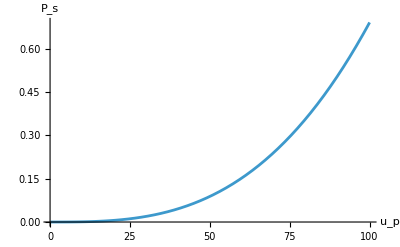

```mathematica
Plot[expr[up],{up,0.1,100},AxesLabel->{"u_p","P_s"},PlotRange->All]
```

```mathematica
Simplify[(-R Log[(4 R T1+(1+k) upiss^2+√(16 k R T1 upiss^2+(1+k)^2 upiss^4))/(4 R T1)]+cp Log[(4 k R T1+(-1+k)^2 upiss^2-√(16 k R T1 upiss^2+(1+k)^2 upiss^4)+k √(16 k R T1 upiss^2+(1+k)^2 upiss^4))/(4 k R T1)]/.upiss->rdot/A)]
```

-R Log[(((1+k) rdot^2)/A^2+4 R T1+√(((1+k)^2 rdot^4)/A^4+(16 k R rdot^2 T1)/A^2))/(4 R T1)]+cp Log[(((-1+k)^2 rdot^2)/A^2+4 k R T1-√(((1+k)^2 rdot^4)/A^4+(16 k R rdot^2 T1)/A^2)+k √(((1+k)^2 rdot^4)/A^4+(16 k R rdot^2 T1)/A^2))/(4 k R T1)]

```mathematica
W = Sqrt[k*R*T1]*Sqrt[((k+1)/(2*k))*(pr-1)+1]
```

√(1+((1+k) (-1+pr))/(2 k)) √(k R T1)

```mathematica
W1=(W/. pr->(4 R T1+upiss^2+k upiss^2+√(16 k R T1 upiss^2+upiss^4+2 k upiss^4+k^2 upiss^4))/(4 R T1))/.upiss->rdot/A//FullSimplify
```

√(k R T1) √(1+(2 (1+k) rdot^2)/(-((1+k) rdot^2)+A^2 √(((1+k)^2 rdot^4+16 A^2 k R rdot^2 T1)/A^4)))

```mathematica
dotps=Simplify[(-R Log[(((1+k) rdot^2)/A^2+4 R T1+√(((1+k)^2 rdot^4)/A^4+(16 k R rdot^2 T1)/A^2))/(4 R T1)]+cp Log[(((-1+k)^2 rdot^2)/A^2+4 k R T1-√(((1+k)^2 rdot^4)/A^4+(16 k R rdot^2 T1)/A^2)+k √(((1+k)^2 rdot^4)/A^4+(16 k R rdot^2 T1)/A^2))/(4 k R T1)])*(L/W1)]
```

(L (-R Log[(((1+k) rdot^2)/A^2+4 R T1+√(((1+k)^2 rdot^4)/A^4+(16 k R rdot^2 T1)/A^2))/(4 R T1)]+cp Log[(((-1+k)^2 rdot^2)/A^2+4 k R T1-√(((1+k)^2 rdot^4)/A^4+(16 k R rdot^2 T1)/A^2)+k √(((1+k)^2 rdot^4)/A^4+(16 k R rdot^2 T1)/A^2))/(4 k R T1)]))/(√(k R T1) √(1+(2 (1+k) rdot^2)/(-((1+k) rdot^2)+A^2 √(((1+k)^2 rdot^4+16 A^2 k R rdot^2 T1)/A^4))))

```mathematica
eqnDotPs [rdot_] :=(L (-R Log[(((1+k) rdot^2)/A^2+4 R T1+√(((1+k)^2 rdot^4)/A^4+(16 k R rdot^2 T1)/A^2))/(4 R T1)]+cp Log[(((-1+k)^2 rdot^2)/A^2+4 k R T1-√(((1+k)^2 rdot^4)/A^4+(16 k R rdot^2 T1)/A^2)+k √(((1+k)^2 rdot^4)/A^4+(16 k R rdot^2 T1)/A^2))/(4 k R T1)]))/(√(k R T1) √(1+(2 (1+k) rdot^2)/(-((1+k) rdot^2)+A^2 √(((1+k)^2 rdot^4+16 A^2 k R rdot^2 T1)/A^4))))
```

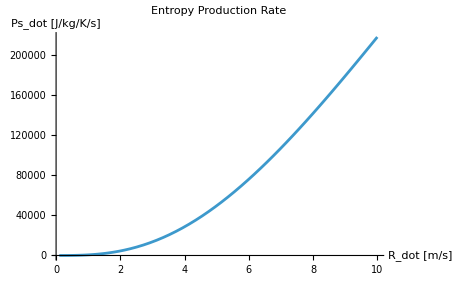

```mathematica
A=0.01;
L=1;
k=5/3;
R=(8.314/4)*1000;
T1=300;
cp=k*R/(k-1);
Plot[eqnDotPs[rdotin]*10^6,{rdotin,0.1,10},PlotLabel->"Entropy Production Rate",AxesLabel->{"R_dot [m/s]", "Ps_dot [J/kg/K/s]"}]
```